```mathematica
PolynomialQuotientRemainder[3x+1,x-4,x]
```

{3,13}

```mathematica
3+13/(x-4)//Together//TraditionalForm
```

(3 x+1)/(x-4)

```mathematica
(3 x+1)/(x-4)//Apart//TraditionalForm
```

13/(x-4)+3

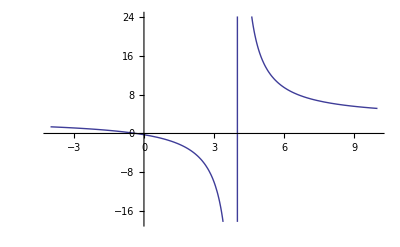

```mathematica
Plot[3+13/(-4+x),{x,-4,10}]
```

```mathematica
f[x]=x/((x-1)(x-2))//ExpandAll//TraditionalForm
```

x/(x^2-3 x+2)

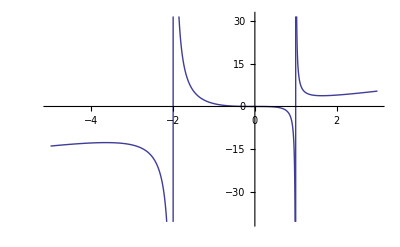

```mathematica
Plot[(2x^3)/((x+2) (x-1)),{x,-5,3}]
```

```mathematica
(2 x^2)/((x+2) (x-1))//ExpandDenominator//TraditionalForm
```

(2 x^2)/(x^2+x-2)

```mathematica
3x+1+(x^2+x-2)/(x^3+3x^2-3x+6)//Together//TraditionalForm
PolynomialQuotientRemainder[x^3,2x^4+1,x]//TraditionalForm;
```

(3 x^4+10 x^3-5 x^2+16 x+4)/(x^3+3 x^2-3 x+6)

```mathematica
f=3x+1+(x+3)/((x-2)(x+1));
f//Together//ExpandDenominator//TraditionalForm
Root[3 x^3-2 x^2-6 x+1==0,x]//N
```

(3 x^3-2 x^2-6 x+1)/(x^2-x-2)

Root::nup: 1 - 6\ x - 2\ x^2 + 3\ x^3 == 0 is not a univariate polynomial.

Root[1-6 x-2 x^2+3 x^3==0,x]

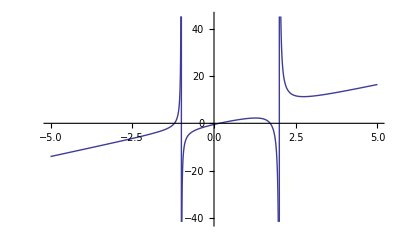

```mathematica
Plot[(1-6 x-2 x^2+3 x^3)/(-2-x+x^2),{x,-5,5}]
```

(2 x^2+2 x)/(x^2+x-2)

{2,4}

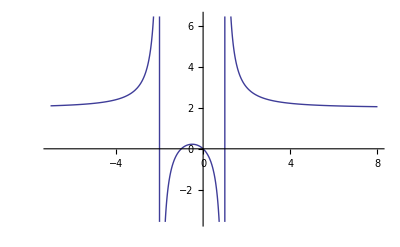

```mathematica
p[x_]:=2x(x+1);
q[x_]:=(x-1)(x+2);
f[x_]:=p[x]/q[x];
f[x]//ExpandNumerator//ExpandDenominator//TraditionalForm
PolynomialQuotientRemainder[p[x],q[x],x]//TraditionalForm
Plot[f[x],{x,-7,8}]
```